## LHC ggPDF generation

Changed my definition to 1/xx by following the equation in the middle of page 159 of Vernon’s Collider Physics book

```mathematica
ggpdf=Table[{rs,NIntegrate[xPDFcv[xx,rs^2,0]xPDFcv[rs^2/13000^2/xx,rs^2,0]/xx,{xx,rs^2/13000^2,1}]},{rs,50,3000,0.1}];
```

```mathematica
ggpdf2=Table[{rs,NIntegrate[xPDFcv[xx,rs^2/4,0]xPDFcv[rs^2/13000^2/xx,rs^2/4,0]/(rs^2/13000^2)/xx,{xx,rs^2/13000^2,1}]},{rs,50,3000,0.1}];
```

```mathematica
ggpdf5=Table[{rs,NIntegrate[xPDFcv[xx,rs^2 4,0]xPDFcv[rs^2/13000^2/xx,rs^2 4,0]/(rs^2/13000^2)/xx,{xx,rs^2/13000^2,1}]},{rs,50,3000,0.1}];
```

ListLogPlot::lpn: ggpdf2 is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLogPlot :: lpn will be suppressed during this calculation.

ListLogPlot::lpn: ggpdf5 is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLogPlot :: lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

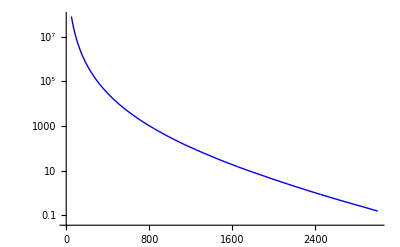
Show[ListLogPlot[ggpdf5,Joined→True,PlotStyle→-Graphics-],ListLogPlot[ggpdf2,Joined→True,PlotStyle→-Graphics-],-Graphics-]

```mathematica
ListLogPlot[ggpdf,Joined->True,PlotStyle->{Blue,Thick}];
ListLogPlot[ggpdf2,Joined->True,PlotStyle->Green];
ListLogPlot[ggpdf5,Joined->True,PlotStyle->Red];
Show[%,%%,%%%]
```

```mathematica
Export["ggpdf13TeVNNPDFLO.dat",ggpdf,"Table"]
```

ggpdf13TeVNNPDFLO.dat

```mathematica
Export["ggpdf13TeVNNPDFLOhalf.dat",ggpdf2,"Table"]
```

ggpdf13TeVNNPDFLOhalf.dat

```mathematica
Export["ggpdf13TeVNNPDFLOdouble.dat",ggpdf5,"Table"]
```

ggpdf13TeVNNPDFLOdouble.dat

## DUNE ggPDF generation

```mathematica
protonmass=0.938;
teamenergy=120;
comsquared=(teamenergy+protonmass)^2-(teamenergy-protonmass)^2;
Sqrt[%]
```

21.2189

Changed my definition to 1/xx by following the equation in the middle of page 159 of Vernon’s Collider Physics book

```mathematica
ggpdf=Table[{rs,NIntegrate[xPDFcv[xx,rs^2,0]xPDFcv[rs^2/comsquared/xx,rs^2,0]/xx,{xx,rs^2/comsquared,1}]},{rs,0.3,Sqrt[comsquared],0.1}];
```

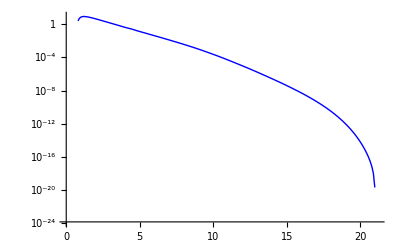

```mathematica
ListLogPlot[ggpdf,Joined->True,PlotStyle->{Blue,Thick}]
```

```mathematica
?alphas
```

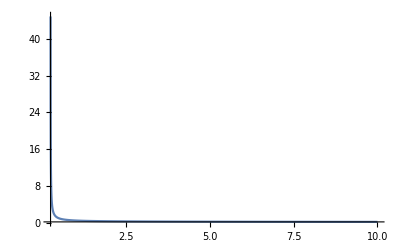

```mathematica
Plot[alphas[x^2,0,0][[1,1]],{x,0.25,10},PlotRange->Full]
```

converting width to parton level rate

```mathematica
decaygluon[x_]:=alphas[x^2,0,0]^3/(32Pi^3) x^3/(1000000)^2
partonrate[x_]:=1/(1/(2x)1/(16Pi)*1/2*8)*1/(2x^2)/(8*8)*(1/2*8)decaygluon[x]
```

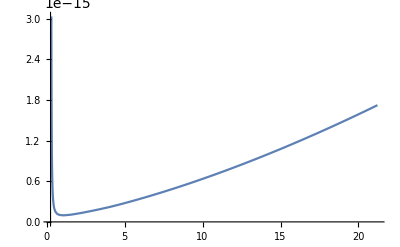

```mathematica
Plot[partonrate[x],{x,0.25,Sqrt[comsquared]}]
```

```mathematica
ggsfunc[x_]:=Interpolation[ggpdf,InterpolationOrder->1][x]//Quiet
```

```mathematica
conversion=0.3894*10^9;(*from GeV^-2 to pb*)
```

```mathematica
colliderrate[x_]:=partonrate[x] ggsfunc[x]
```

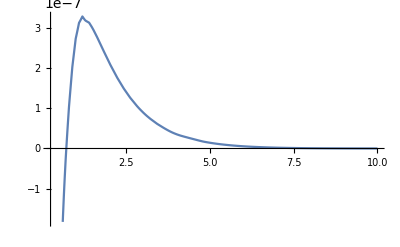

```mathematica
Plot[conversion*colliderrate[x],{x,0.25,10}]
```

```mathematica
ggpdf2=Table[{rs,NIntegrate[xPDFcv[xx,rs^2/4,0]xPDFcv[rs^2/13000^2/xx,rs^2/4,0]/(rs^2/13000^2)/xx,{xx,rs^2/13000^2,1}]},{rs,50,3000,50}];
```

```mathematica
ggpdf5=Table[{rs,NIntegrate[xPDFcv[xx,rs^2 4,0]xPDFcv[rs^2/13000^2/xx,rs^2 4,0]/(rs^2/13000^2)/xx,{xx,rs^2/13000^2,1}]},{rs,50,3000,50}];
```

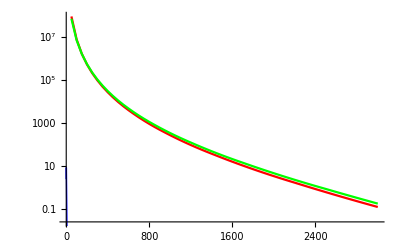

```mathematica
ListLogPlot[ggpdf,Joined->True,PlotStyle->{Blue,Thick}];
ListLogPlot[ggpdf2,Joined->True,PlotStyle->Green];
ListLogPlot[ggpdf5,Joined->True,PlotStyle->Red];
Show[%,%%,%%%]
```

```mathematica
Export["ggpdf13TeVNNPDFLO.dat",ggpdf,"Table"]
```

ggpdf13TeVNNPDFLO.dat